# Finite Rod, Albedo Problem, Isotropic Scattering

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Exponential Random Flight

## Notation

α - single-scattering albedo
Σt - extinction coefficient
x - position coordinate in rod (source at x = 0)
a - length of the rod

## Analytic solutions

### Reflectance/Transmittance

```mathematica
R[a_,α_,Σt_]:=α/(2 √(1-α)Coth[Σt a √(1-α)]-α+2)
```

```mathematica
T[a_,α_,Σt_]:=(2 √(1-α))/(2 √(1-α)Cosh[Σt a √(1-α)]-(α-2)Sinh[Σt a √(1-α)])
```

```mathematica
R[a_,α_,Σt_,n_]:=α^n(SeriesCoefficient[R[a,A,Σt],{A,0,n}]/.A->α);
T[a_,α_,Σt_,n_]:=α^n(SeriesCoefficient[T[a,A,Σt],{A,0,n}]/.A->α)
```

### ‘Radiance’

```mathematica
LR[x_,α_,Σt_,a_]:=(2 (-1+α) Cosh[(a-x) √(1-α) Σt]+√(1-α) (-2+α) Sinh[(a-x) √(1-α) Σt])/(2 (-1+α) Cosh[a √(1-α) Σt]+√(1-α) (-2+α) Sinh[a √(1-α) Σt])
```

```mathematica
LL[x_,α_,Σt_,a_]:=-(√(1-α) α Sinh[(a-x) √(1-α) Σt])/(2 (-1+α) Cosh[a √(1-α) Σt]+√(1-α) (-2+α) Sinh[a √(1-α) Σt])
```

### Fluence

```mathematica
ϕ[x_,α_,Σt_,a_]:=LR[x,α,Σt,a]+LL[x,α,Σt,a]
```

## Monte Carlo comparisons

```mathematica
ppoints[xs_,dx_,maxx_,Σt_]:=Table[{dx(i-1)+0.5dx,(1/Σt)xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
fs=FileNames["code/rod/finiterod/albedoProblem/data/finiterod_albedoproblem_isotropicscatter_exp_c0.7_mut1_*"];
```

### Reflectance/Transmittance

```mathematica
MCR[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,5]];
{a,data[[3,4]]}
];
MCT[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,5]];
{a,data[[4,4]]}
]
```

```mathematica
Rs=Table[MCR[f],{f,fs}];
Ts=Table[MCT[f],{f,fs}];
```

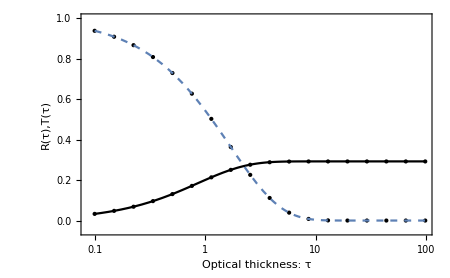

```mathematica
vizfiniterodRTiso=Show[
ListLogLinearPlot[Rs,PlotRange->{-0.05,1},PlotStyle->{PointSize[Medium],Black}],
ListLogLinearPlot[Ts,PlotRange->{-0.05,1},PlotStyle->{PointSize[Medium],Black}],
LogLinearPlot[R[a,0.7,1],{a,0.1,100},PlotStyle->Black],
LogLinearPlot[T[a,0.7,1],{a,0.1,100},PlotStyle->Dashed],
ImageSize->450,
Frame->True,FrameLabel->{{"R(τ),T(τ)",},{"Optical thickness: τ","Total Reflectance/Transmittance (R/T): isotropically-scattering finite rod"}}
]
```

```mathematica
fs2=FileNames["code/rod/finiterod/albedoProblem/data/finiterod_albedoproblem_isotropicscatter_exp_*length2.6*"];
```

```mathematica
MCR2[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,3]];
{a,data[[3,4]]}
];
MCT2[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,3]];
{a,data[[4,4]]}
]
```

```mathematica
Rs2=Table[MCR2[f],{f,fs2}];
Ts2=Table[MCT2[f],{f,fs2}];
```

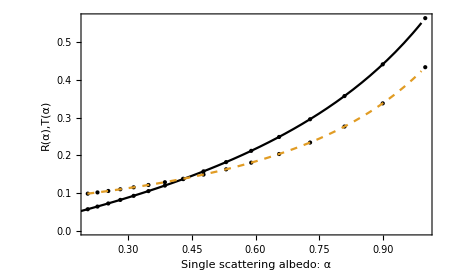

```mathematica
a=2.6;
mut=1;
finiterodvarycplot=Show[
ListPlot[Rs2,PlotStyle->{PointSize[Medium],Black}],
ListPlot[Ts2,PlotStyle->{PointSize[Medium],Black}],
Plot[{R[a,c,mut],T[a,c,mut]},{c,0.01,.99},PlotRange->{0,.7},PlotStyle->{Black,Dashed}],
ImageSize->450,
Frame->True,FrameLabel->{{"R(α),T(α)",},{"Single scattering albedo: α","Total Reflectance/Transmittance (R/T): isotropically-scattering finite rod"}}
]
```

### Select simulation

```mathematica
fs=FileNames["code/rod/finiterod/albedoProblem/data/finiterod_albedoproblem_isotropicscatter_exp_c0.7_mut0.8*"]
filename=fs[[1]];
data=Import[filename,"Table"];
Σt=data[[1,11]];
α=data[[2,3]];
a=data[[2,5]];
dx=data[[2,7]];
numcollorders=data[[2,11]];
nummoments=data[[2,13]];
g=data[[1,-1]];

densmom=data[[11]];
```

{code/rod/finiterod/albedoProblem/data/finiteRod_albedoproblem_isotropicscatter_exp_c0.7_mut0.8_length2.2.txt}

### Internal Distributions

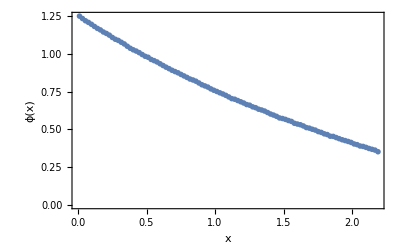

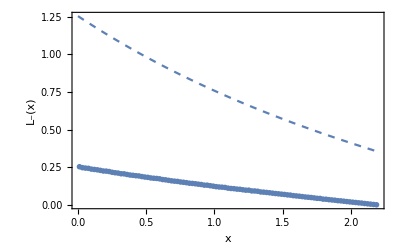

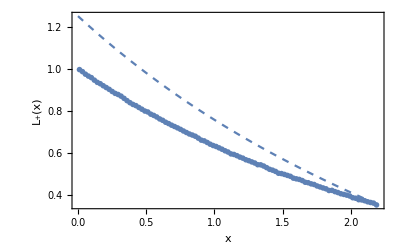

```mathematica
pointsCL = data[[10]];
(* divide by Σt to convert collision density into L *)
plotpointsCL=ppoints[pointsCL,dx,a,Σt];
pointsCR = data[[12]];
plotpointsCR=ppoints[pointsCR,dx,a,Σt];
(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=ppoints[pointsCL+pointsCR,dx,maxx,Σt];

plotϕ=Show[
ListPlot[plotpointsϕ,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[ϕ[x,α,Σt,a],{x,0,a},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ[x],},{x,"Finite rod, albedo problem, isotropic scattering, fluence ϕ[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", a = "<>ToString[a]}}
]

plotLL=Show[
ListPlot[plotpointsCL,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LL[x,α,Σt,a],{x,0,a},PlotRange->All],
Plot[ϕ[x,α,Σt,a],{x,0,a},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubMinus[L][x],},{x,"Finite rod, albedo problem, isotropic scattering, L_-[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", a = "<>ToString[a]}},PlotRange->All
]

plotLR=Show[
ListPlot[plotpointsCR,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LR[x,α,Σt,a],{x,0,a},PlotRange->All],
Plot[ϕ[x,α,Σt,a],{x,0,a},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubPlus[L][x],},{x,"Finite rod, albedo problem, isotropic scattering, L_+[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", a = "<>ToString[a]}},PlotRange->All
]
```

### Nth-scattered Reflectance

```mathematica
Rs=N[{data[[6]]}];
ns=Table[n,{n,0,numcollorders-1}];
analytic=Table[R[a,α,Σt,n],{n,ns}];
j=Join[{ns},{analytic},Rs];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[j]]
]
```

n | analytic | MC
0 | 0. | 0.
1 | 0.16982 | 0.169702
2 | 0.0530554 | 0.0529898
3 | 0.0188762 | 0.0188996
4 | 0.00696225 | 0.0069549
5 | 0.00259536 | 0.0025943
6 | 0.00097059 | 0.0009506
7 | 0.000363326 | 0.0003673
8 | 0.000136046 | 0.0001358
9 | 0.0000509468 | 0.000049

### Nth-scattered Transmittance

```mathematica
Ts=N[{data[[8]]}];
ns=Table[n,{n,0,numcollorders-1}];
analytic=Table[T[a,α,Σt,n],{n,ns}];
j=Join[{ns},{analytic},Ts];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[j]]
]
```

n | analytic | MC
0 | 0.172045 | 0.172147
1 | 0.10598 | 0.10578
2 | 0.0460752 | 0.0460467
3 | 0.0180818 | 0.0179851
4 | 0.00687125 | 0.0068802
5 | 0.00258492 | 0.0025857
6 | 0.000969392 | 0.0009688
7 | 0.000363189 | 0.0003783
8 | 0.000136031 | 0.0001391
9 | 0.000050945 | 0.0000494

### Nth order fluence/density

```mathematica
nthϕ=data[[16+numcollorders+1;;16+2numcollorders]];
```

0.49 (-0.0861343 Cosh[1.76-0.8 x]+0.0516135 x Cosh[1.76-0.8 x]+0.0137636 x^2 Cosh[1.76-0.8 x]+0.129782 Sinh[1.76-0.8 x]+0.0172045 x Sinh[1.76-0.8 x]+0.0137636 x^2 Sinh[1.76-0.8 x])

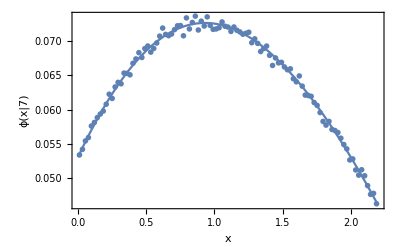

```mathematica
(* choose order:*)
n=2;

Clear[c];
phin=SeriesCoefficient[ϕ[x,c,Σt,a],{c,0,n}] α^n
plotphin=Show[
ListPlot[ppoints[nthϕ[[n+2]],dx,a,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[phin,{x,0,a},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ["x|7"],},{x,"Semi-Infinite Rod, isotropic point, isotropic scattering, ϕ[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
]
```